Power::infy: 無限式1/0.が見付かりました．

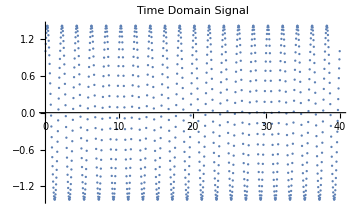
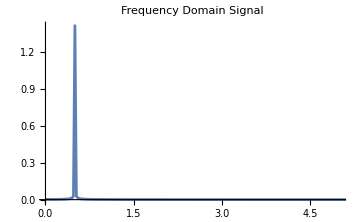
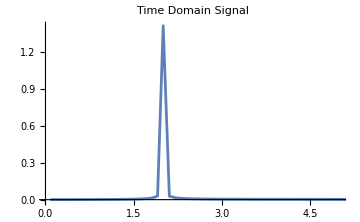

```mathematica
(*check*)
ClearAll["Global`*"];
ClearAll["Global`*"];
T=2.;
n=1000;
span=20*T;
data=Table[{t,Sin[t*2 π/T]+Cos[t*2 π/T]},{t,Subdivide[0,span,n-1]}];
(*Calculate the FFT magnitude without any additional normalization*)
fft=2*Abs@Fourier[data[[;;-1,2]],FourierParameters->{-1, 1}];

(*Calculate the frequency bins*)
Fs=n/span;
freq=Table[i*Fs/n,{i,0,n/2-1}]; (*Positive frequencies*)

{ListPlot[data,ImageSize->Medium,PlotLabel->"Time Domain Signal"],
ListPlot[Transpose[{freq,fft[[;;n/2]]}],Joined->True,PlotRange->{{0,5},All},ImageSize->Medium,PlotLabel->"Frequency Domain Signal"],
ListPlot[Transpose[{1/freq,fft[[;;n/2]]}],Joined->True,PlotRange->{{0,5},All},ImageSize->Medium,PlotLabel->"Time Domain Signal"]}
```

```mathematica
ClearAll["Global`*"];
storage="/Volumes/home/BEM/";
case="moon_pool_large_a0d8_";
(*case="moon_pool_no_a0d8_";*)
data[5.0]=Import[storage<>case<>"T5d0_h80/result.json"];
data[5.5]=Import[storage<>case<>"T5d5_h80/result.json"];
data[6.0]=Import[storage<>case<>"T6d0_h80/result.json"];
data[6.5]=Import[storage<>case<>"T6d5_h80/result.json"];
data[7.0]=Import[storage<>case<>"T7d0_h80/result.json"];
data[7.5]=Import[storage<>case<>"T7d5_h80/result.json"];
data[8.0]=Import[storage<>case<>"T8d0_h80/result.json"];
data[8.5]=Import[storage<>case<>"T8d5_h80/result.json"];
data[9.0]=Import[storage<>case<>"T9d0_h80/result.json"];
data[9.5]=Import[storage<>case<>"T9d5_h80/result.json"];
data[10.0]=Import[storage<>case<>"T10d0_h80/result.json"];
(*Recreate*)
dt=0.01;
min=0;
max=100;
Do[
DATA=data[T];
Time[T]=Table[t,{t,min,max,dt}];
Module[{tmp},
tmp=Interpolation[Transpose[{"time"/.DATA,("floatingbody_pitch"/.DATA)}]];
intpPitch[T]=Table[tmp[t],{t,min,max,dt}];
];
Module[{tmp},
tmp=Interpolation[Transpose[{"time"/.DATA,(("floatingbody_COM"/.DATA)ᵀ[[3]]-75)}]];
intpHeave[T]=Table[tmp[t],{t,min,max,dt}];
];
Module[{tmp},
tmp=Interpolation[Transpose[{"time"/.DATA,(("floatingbody_COM"/.DATA)ᵀ[[1]]-200)}]];
intpSurge[T]=Table[tmp[t],{t,min,max,dt}];
]
,{T,5.0,10.0,.5}]

dataLen[T_]:=Length[Table[t,{t,min,max,dt}]];

Pitch[T_]:=intpPitch[T];
Heave[T_]:=intpHeave[T];
Surge[T_]:=intpSurge[T];

fftPitch[T_]:=With[{n=Length[Time[T]]},Return[2*Abs@Fourier[intpPitch[T][[;;-1]],FourierParameters->{-1, 1}]];];
fftHeave[T_]:=With[{n=Length[Time[T]]},Return[2*Abs@Fourier[intpHeave[T][[;;-1]],FourierParameters->{-1, 1}]];];
fftSurge[T_]:=With[{n=Length[Time[T]]},Return[2*Abs@Fourier[intpSurge[T][[;;-1]],FourierParameters->{-1, 1}]];];

getPeriod[T_]:=1/Table[i/(max-min),{i,Length[fftPitch[T]]}];
getTime[T_]:=Module[{},Return[(Time[T])];];
(*ListPlot[Table[Transpose[{Table[i/(max-min),{i,Length[fftPitch[T]]}],fftPitch[T]}][[;;20]],{T,5.5,10.,0.5}],PlotRange->All,Joined->True]*)
```

Import::nffil: Importの最中にファイル/Volumes/home/BEM/moon_pool_large_a0d8_T8d0_h80/result.jsonが見付かりませんでした．

Import::nffil: Importの最中にファイル/Volumes/home/BEM/moon_pool_large_a0d8_T10d0_h80/result.jsonが見付かりませんでした．

InterpolatingFunction::dmval: 入力値{0.}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{0.01}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{0.02}は補間関数のデータ範囲外です．外挿が使用されます．

General::stop: この計算中に，InterpolatingFunction::dmvalのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Interpolation::inhr: 要求された次数が高すぎます．次数は{1}に削減されました．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partw: Transpose[floatingbody_COM/.$Failed]の部分3は存在しません．

Interpolation::inhr: 要求された次数が高すぎます．次数は{1}に削減されました．

General::stop: この計算中に，Interpolation::inhrのこれ以上の出力は表示されません．

Part::partw: Transpose[floatingbody_COM/.$Failed]の部分3は存在しません．

```mathematica
(*dataLen[T_]:=Length["time"/.data[T]];

Pitch[T_]:=("floatingbody_pitch"/.data[T])[[;;-1]];
Heave[T_]:=("floatingbody_COM"/.data[T])ᵀ[[3]]-75;
Surge[T_]:=(("floatingbody_COM"/.data[T])ᵀ[[1]]-200)[[;;-1]];

fftPitch[T_]:=With[{n=Length["time"/.data[T]]},Return[2*Abs@Fourier[("floatingbody_pitch"/.data[T])[[;;-1]],FourierParameters->{-1, 1}]];];
fftHeave[T_]:=With[{n=Length["time"/.data[T]]},Return[2*Abs@Fourier[(("floatingbody_COM"/.data[T])ᵀ[[3]]-75)[[;;-1]],FourierParameters->{-1, 1}]];];
fftSurge[T_]:=With[{n=Length["time"/.data[T]]},Return[2*Abs@Fourier[(("floatingbody_COM"/.data[T])ᵀ[[1]]-200)[[;;-1]],FourierParameters->{-1, 1}]];];
(*getPeriod[data_]:=With[{timelist="time"/.data,n=Length[timelist],dt=0.2},Return@Table[(i/(n*dt))^-1,{i,1,n,1}]];*)
getPeriod[T_]:=Module[{t,n},t="time"/.data[T];n=Length[t];Return@Table[(i/(n*(If[i+1>n,t[[i]]-t[[i-1]],t[[i+1]]-t[[i]]])))^-1,{i,1,n,1}]];
getTime[T_]:=Module[{},Return[("time"/.data[T])];];*)
```

```mathematica
(*Do[data75[[i]][[2]]=data75[[i]][[2]][[;;547]],{i,1,Length[data75]}]*)
```

```mathematica
Column@data[5.0][[;;,1]]
```

floatingbody_accel
floatingbody_velocity
floatingbody_COM
floatingbody_force
floatingbody_torque
floatingbody_EK
floatingbody_EP
floatingbody_area
floatingbody_pitch
floatingbody_roll
floatingbody_yaw
time
water_E
water_EK
water_EP
water_volume

```mathematica
(*Peridos to check*)
Ts={(*5.0,*)5.5,6.0,6.5,7.0,(*7.5,8.0,*)8.5,9.0,9.5(*,10.*)};
```

```mathematica
commonOptions2D=Sequence[
AspectRatio->1/2,
Joined->True,
Frame->True,
PlotStyle->Table[{ColorData[90,"ColorList"][[i]],{Dashed,Normal}[[Mod[i,2]+1]]},{i,1,10}],
ImageSize->Large,
AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
FrameStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
LabelStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
PlotLegends->Placed[LineLegend[Table[T,{T,Ts}],LegendLabel->"Incident wave period [s]",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Top],
FrameStyle->Black];
commonOptions3D=Sequence[TicksStyle->Black,ImageSize->Medium,AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}]];
```

## Surge

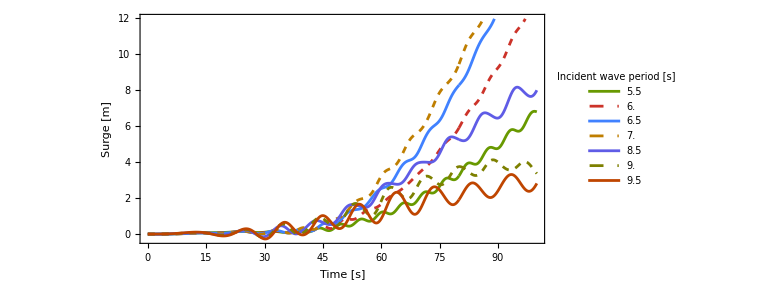
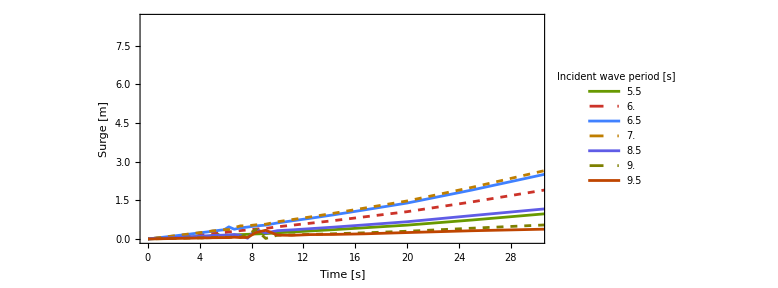

```mathematica
{ListPlot[Table[Transpose[{getTime[T],Surge[T]}][[;;Round[dataLen[T]]]],{T,Ts}]
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Surge [m]"}
,PlotLegends->Table[T,{T,Ts}]
]
,
ListPlot[Table[Transpose[{getPeriod[T],fftSurge[T]}][[;;Round[dataLen[T]/2]]],{T,Ts}]
,PlotRange->{{0,30},All}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Surge [m]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
]}
```

## Heave

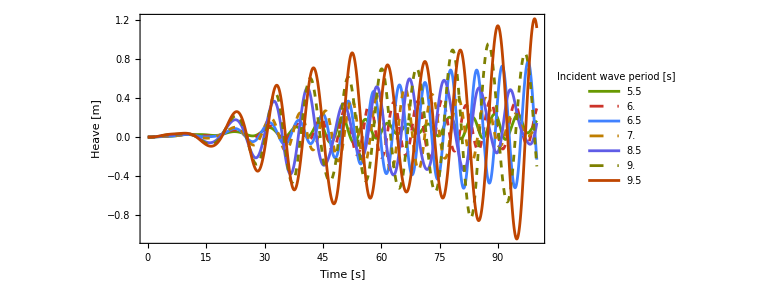
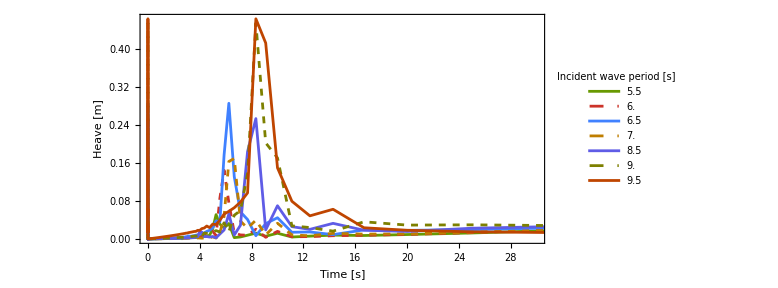

```mathematica
{
ListPlot[Table[Transpose[{getTime[T],Heave[T]}],{T,Ts}]
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Heave [m]"}
,PlotLegends->Table[T,{T,Ts}]
]
,
ListPlot[Table[Transpose[{getPeriod[T],fftHeave[T]}],{T,Ts}]
,PlotRange->{{0,30},All}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Heave [m]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
]
}
```

## Pitch

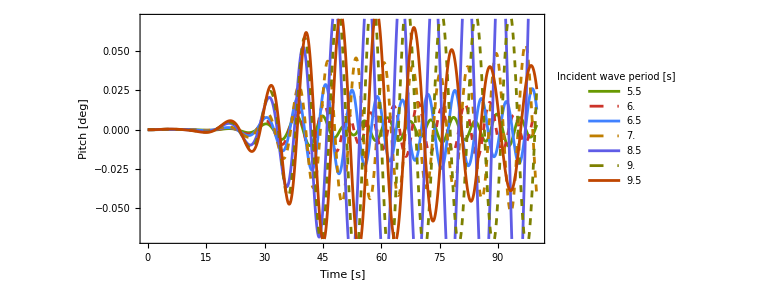
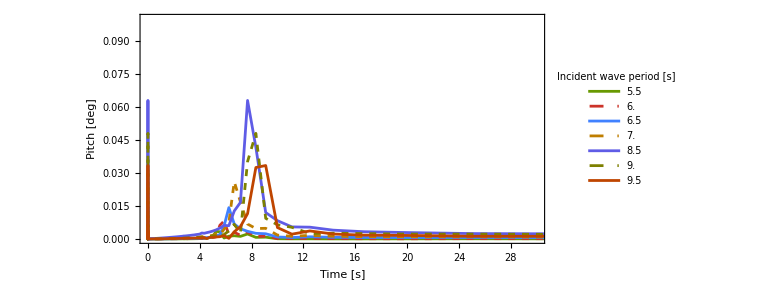

```mathematica
{
ListPlot[Table[Transpose[{getTime[T],Pitch[T]}],{T,Ts}]
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Pitch [deg]"}
,PlotLegends->Table[T,{T,Ts}]
]
,
ListPlot[Table[Transpose[{getPeriod[T],fftPitch[T]}],{T,Ts}]
,PlotRange->{{0,30},{0,0.1}}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Pitch [deg]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
]
}
```